## Simplified form of the triaxial potential V(q)

```mathematica
IF[moi_]:=1/(2*moi);
j1[j_,theta_]:=j *Cos[theta*π/180];
j2[j_,theta_]:=j *Sin[theta*π/180];
AFct[I_,I1_,I2_,j_,theta_]:=IF[I2](1-j2[j,theta]/I)-IF[I1];
uFct[I_,I1_,I2_,I3_,j_,theta_]:=(IF[I3]-IF[I1])/AFct[I,I1,I2,j,theta];
v0Fct[I_,I1_,I2_,j_,theta_]:=(-IF[I1]*j1[j,theta])/AFct[I,I1,I2,j,theta];
kFct[I_,I1_,I2_,I3_,j_,theta_]:=If[uFct[I,I1,I2,I3,j,theta]≤0,Sqrt[Abs[uFct[I,I1,I2,I3,j,theta]]],Sqrt[uFct[I,I1,I2,I3,j,theta]]];
```

## Parameter set

```mathematica
(*{SPIN,I1,I2,I3,j,θ}*)
pSet[theta_]:={9.5,85,100,65,5.5,theta};
```

## Potential expression

```mathematica
VRotor[q_,I_,I1_,I2_,I3_,j_,θ_]:=(I(I+1)kFct[I,I1,I2,I3,j,θ]^2+v0Fct[I,I1,I2,j,θ]^2)*Sin[JacobiAmplitude[q,kFct[I,I1,I2,I3,j,θ]^2]]^2+(2I+1)*v0Fct[I,I1,I2,j,θ]*Cos[JacobiAmplitude[q,kFct[I,I1,I2,I3,j,θ]^2]]*√(1-kFct[I,I1,I2,I3,j,θ]^2*Sin[JacobiAmplitude[q,kFct[I,I1,I2,I3,j,θ]^2]]^2);
```

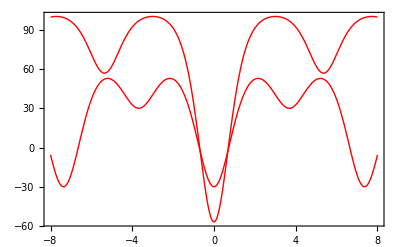

```mathematica
plot[theta_]:=Plot[VRotor[q,pSet[theta][[1]],pSet[theta][[2]],pSet[theta][[3]],pSet[theta][[4]],pSet[theta][[5]],pSet[theta][[6]]],{q,-8,8},Frame->True,Axes->False,PlotStyle->{Red,Thick},PlotRange->All];
Show[plot[-80],plot[100]]
```

```mathematica
params[theta_]:=Print[kFct[pSet[theta][[1]],pSet[theta][[2]],pSet[theta][[3]],pSet[theta][[4]],pSet[theta][[5]],pSet[theta][[6]]],"\n",v0Fct[pSet[theta][[1]],pSet[theta][[2]],pSet[theta][[3]],pSet[theta][[5]],pSet[theta][[6]]]];
theta=-80;
thetaChiral=theta+180;
```

```mathematica
params[theta]
Print[VRotor[0,pSet[theta][[1]],pSet[theta][[2]],pSet[theta][[3]],pSet[theta][[4]],pSet[theta][[5]],pSet[theta][[6]]]]
```

0.958907
-2.8541

-57.082

```mathematica
params[thetaChiral]
Print[VRotor[0,pSet[thetaChiral][[1]],pSet[thetaChiral][[2]],pSet[thetaChiral][[3]],pSet[thetaChiral][[4]],pSet[thetaChiral][[5]],pSet[thetaChiral][[6]]]]
```

0.696303
-1.50492

-30.0984

```mathematica
Do[Print[q,"    ",VRotor[q,pSet[theta][[1]],pSet[theta][[2]],pSet[theta][[3]],pSet[theta][[4]],pSet[theta][[5]],pSet[theta][[6]]]],{q,-8,8,1.5}]
```

-8.    100.045+0. ⅈ

-6.5    87.5252+0. ⅈ

-5.    62.5051+0. ⅈ

-3.5    98.8442+0. ⅈ

-2.    91.5956+0. ⅈ

-0.5    -23.8547+0. ⅈ

1.    34.2759+0. ⅈ

2.5    98.7554+0. ⅈ

4.    92.4922+0. ⅈ

5.5    57.9397+0. ⅈ

7.    96.7302+0. ⅈ

```mathematica
Do[Print[q,"    ",VRotor[q,pSet[thetaChiral][[1]],pSet[thetaChiral][[2]],pSet[thetaChiral][[3]],pSet[thetaChiral][[4]],pSet[thetaChiral][[5]],pSet[thetaChiral][[6]]]],{q,-8,8,1.5}]
```

-8.    -5.63492+0. ⅈ

-6.5    9.46569+0. ⅈ

-5.    52.1273+0. ⅈ

-3.5    31.0277+0. ⅈ

-2.    52.445+0. ⅈ

-0.5    -13.8502+0. ⅈ

1.    17.9229+0. ⅈ

2.5    50.6139+0. ⅈ

4.    32.7966+0. ⅈ

5.5    50.989+0. ⅈ

7.    -20.933+0. ⅈ